## Full phase diagram in three-level system

```mathematica
ham[Δ_,Ω_,γ_]:=Evaluate[{{Δ-I γ,-1,Ω},{-1,Δ+I γ,Ω},{Ω,Ω,0}}];
ham[Δ,Ω,γ]//MatrixForm
```

(-ⅈ γ+Δ | -1 | Ω
-1 | ⅈ γ+Δ | Ω
Ω | Ω | 0)

```mathematica
EP2Surf[Δ_,Ω_,γ_]:=Simplify[Discriminant[Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]]
```

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e];
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];


x1 =Reduce[-Det[ham[-3/4,1/2,((γ^(1/3))-3^(3/2)/4)]-IdentityMatrix[3]e]==0,e,Cubics->True][[1]][[2]];
x2=Reduce[Reduce[-Det[ham[-1,3/5,γ]-IdentityMatrix[3]e]==0,e,Cubics->True][[3]][[2]]==0,γ]
Simplify[Series[x1,{γ,0,1}]];
```

γ==-(3 √2)/5||γ==(3 √2)/5

```mathematica
ReEquSurf=Numerator@Simplify[(a1-3a0/a2)/2-(a2/3)^2]
```

Δ^3+27 Ω^2+9 Δ (-1+γ^2+Ω^2)

```mathematica
EP2Surf[Δ,Ω,0]
```

4 (1+Δ-Ω^2)^2 (1-2 Δ+Δ^2+8 Ω^2)

```mathematica
P1=Show[ContourPlot3D[Evaluate[EP2Surf[Δ,Ω,γ]]==0,{Δ,-1.2,0.3},{Ω,0,1.5},{γ,0,3},PlotPoints->100,Mesh->None,PlotRange->All,ContourStyle->Directive[Lighter@Blue,Opacity[0.7],Lighting->"Accent"]],
Frame->True,AxesLabel->{"Δ","Ω","γ"},Boxed->True,AxesStyle->Directive[Black,18],ImageSize->300]
Surf0=ContourPlot3D[γ==0,{Δ,-1.2,0.3},{Ω,0,1.5},{γ,0,3},RegionBoundaryStyle->None,ContourStyle->{Lighter@Orange,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
SurfOme=ContourPlot3D[Ω==3/10,{Δ,-1.2,0.3},{Ω,0,1.5},{γ,0,3},RegionBoundaryStyle->None,ContourStyle->{Lighter@Orange,Opacity[0.3]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
Show[P1,Surf0,PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
RealSurf=ContourPlot3D[Δ^3+27 Ω^2+9 Δ (-1+γ^2+Ω^2)==0,{Δ,-1.2,0.3},{Ω,0,1.5},{γ,0,3},RegionFunction->Function[{x,y,z},Evaluate[EP2Surf[x,y,z]<0]],RegionBoundaryStyle->None,ContourStyle->{Lighter@Green,Opacity[0.5]},BoundaryStyle->None,Mesh->None,PerformanceGoal->"Quality",PlotPoints->100];
Show[P1,RealSurf,SurfOme,PlotRange->All]
```

-Graphics3D-

```mathematica
EP3EqG=FactorList[Simplify[Resultant[EP2Surf[Δ,Ω,γ],ReEquSurf,γ]]];
EP3G0=FactorList[EP2Surf[Δ,Ω,0]];
MatrixForm[EP3EqG];
EP3G0//MatrixForm;
EP3ProjLineG=EP3EqG[[2,1]]
EP3G0[[2,1]]
```

4 Δ^3+27 Ω^2+27 Δ Ω^2

1+Δ-Ω^2

```mathematica
P3=Show[ContourPlot[{EP3ProjLineG==0,EP3G0[[2,1]]==0},{Δ,-1.3,0.3},{Ω,0,1.5},PlotPoints->50,ContourStyle->{{RGBColor[.8,0,0,1],Thickness[0.01]},{RGBColor[0,.3,.7,1],Thickness[0.01]}}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0.3,0},{-1.3,0}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{0,0},{0,3.02}}]}],
Graphics[{Gray,Thickness[0.01],Dashed,Line[{{-1.01,0},{-1.01,3.02}}]}]];
```

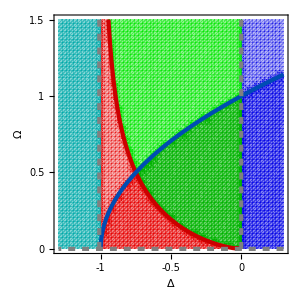

```mathematica
P4=Show[
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG<0&&Ω>0,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG<0&&Δ>-1,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&0<Δ<0.3,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0&&0<Δ<0.3,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.3]}],
RegionPlot[EP3G0[[2,1]]<0&&EP3ProjLineG>0 &&Δ<0,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.9,0,.45]}],
RegionPlot[EP3G0[[2,1]]>0&&EP3ProjLineG>0&&Δ<0,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],
RegionPlot[Δ<-1,{Δ,-1.3,0.3},{Ω,0,1.5},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5](*,GrayLevel[0.75]*)}],
P3,Frame->True,FrameLabel->{"Δ","Ω"},PlotTheme->"Scientific",FrameTicks->{{{0,0.5,1,1.5},None},{{-1,-0.5,0},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,1.5}},ImageSize->300]
```

## 2D Ω slice cut

```mathematica
Ω0=3/10;
Ω1=2+2/5;
```

```mathematica
cs01=Flatten[Δ/.Solve[(1+Δ-Ω^2/.Ω->Ω0)==0,Δ]][[1]];
cs02=Flatten[Δ/.Solve[(4 Δ^3+27 Ω^2+27 Δ Ω^2/.Ω->Ω0)==0,Δ]][[1]];
cs11=Flatten[Δ/.Solve[(1+Δ-Ω^2/.Ω->Ω1)==0,Δ]][[1]];
cs12=Flatten[Δ/.Solve[(4 Δ^3+27 Ω^2+27 Δ Ω^2/.Ω->Ω1)==0,Δ]][[1]];
```

```mathematica
0.975-0.15
```

0.825

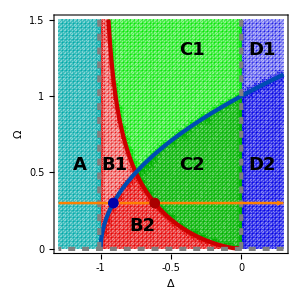

```mathematica
P5=Show[P4,
Graphics[{Text[Style["C2",FontFamily->"Arial",Bold,18],{-0.35,1.1/2}]}],
Graphics[{Text[Style["C1",FontFamily->"Arial",Bold,18],{-0.35,2.6/2}]}],
Graphics[{Text[Style["B1",FontFamily->"Arial",Bold,18],{-0.9,1.1/2}]}],
Graphics[{Text[Style["B2",FontFamily->"Arial",Bold,18],{-0.7,0.3/2}]}],
Graphics[{Text[Style["A",FontFamily->"Arial",Bold,18],{-1.15,1.1/2}]}],
Graphics[{Text[Style["D1",FontFamily->"Arial",Bold,18],{0.15,2.6/2}]}],
Graphics[{Text[Style["D2",FontFamily->"Arial",Bold,18],{0.15,1.1/2}]}],
With[{Ω=Ω0},Graphics[{Orange,Thickness[0.006],Arrow[{{-1.3,Ω},{0.3,Ω}}]}]],
With[{Δ=cs01},Graphics[{Dashed,Darker@Blue,PointSize[0.025],Point[{{cs01,Ω0},{cs01,Ω0}}]}]],With[{Δ=cs02},Graphics[{Dashed,Darker@Red,PointSize[0.025],Point[{{cs02,Ω0},{cs02,Ω0}}]}]]]
```

```mathematica
compcond=Simplify[Discriminant[Det[ham[Δ,Ω0,γ]-IdentityMatrix[3]e],e]]
```

-4 γ^6+γ^4 (354/25-8 Δ^2)+((91+100 Δ)^2 (43-50 Δ+25 Δ^2))/62500+γ^2 (-10443/625-(162 Δ)/25+(62 Δ^2)/5-4 Δ^4)

```mathematica
Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e]
a2=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,2];
a1=Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,1];
a0=-Coefficient[Collect[-Det[ham[Δ,Ω,γ]-IdentityMatrix[3]e],e],e,0];
realcond0=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω0}
realcond1=(a1-3a0/a2)/2-(a2/3)^2/.{Ω->Ω1}
```

e^3-2 e^2 Δ+Ω^2/2+(Δ Ω^2)/2+e (-1+γ^2+Δ^2-Ω^2/2)

-(4 Δ^2)/9+1/2 (-59/50+γ^2-(3 (-9/50-(9 Δ)/50))/(2 Δ)+Δ^2)

-(4 Δ^2)/9+1/2 (-97/25+γ^2-(3 (-72/25-(72 Δ)/25))/(2 Δ)+Δ^2)

```mathematica
gs=γ/.Solve[(-(4 Δ^2)/9+1/2 (-59/50+γ^2-(3 (-9/50-(9 Δ)/50))/(2 Δ)+Δ^2)/.{Δ->cs02})==0,γ][[2]]
```

(√(-243+819 Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936-100 (Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936)^3))/(30 √(Root-0.616Root[243+243 #1+400 #1^3&,1]-0.6157336413227936))

```mathematica
P6=Show[ContourPlot[compcond==0,{Δ,-1.3,0.3},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Blue,Opacity[1],(*Black*),Thickness[0.01]]],
ContourPlot[realcond0==0,{Δ,0,cs02},{γ,0,3},PlotPoints->100,ContourStyle->Directive[Lighter@Green,Opacity[1],(*Black,Dashed,*)Thickness[0.01]]],
With[{Δ=cs01},Graphics[{Dashed,Darker@Blue,PointSize[0.025],Point[{{cs01,0}}]}]],With[{Δ=cs02},Graphics[{Dashed,Darker@Red,PointSize[0.025],Point[{{cs02,N[gs]}}]}]],
With[{Δ=-1},Graphics[{Black,Thickness[0.01],Arrow[{{-1.3,Ω},{0.3,Ω}}]}]],
Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,-0.5,-1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
```

-Graphics-

Export::nodir: Directory C:\Users\phykai\Nutstore Files\Research\Paper_ReEntryPolariton\Paper\Figs\ does not exist.

Export::noopen: Cannot open /Users/phykai/Nutstore Files/Research/Paper_ReEntryPolariton/Paper/Figs/Fig3c.png.

$Failed

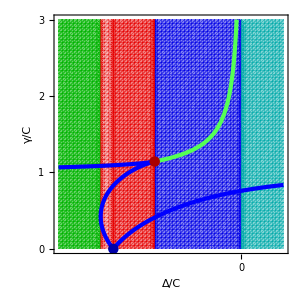

```mathematica
P7=Show[RegionPlot[Δ<-1,{Δ,-1.3,0.3},{γ,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0.7,0,.6]}],RegionPlot[cs02<Δ<0,{Δ,-1.3,0.3},{γ,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[0,0,.9,.5]}],RegionPlot[cs01<Δ<cs02,{Δ,-1.3,0.3},{γ,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.5]}],RegionPlot[-1<Δ<cs01,{Δ,-1.3,0.3},{γ,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{RGBColor[.9,0,0,.3]}],RegionPlot[0<Δ<0.3,{Δ,-1.3,0.3},{γ,0,3},BoundaryStyle->None,PlotPoints->60,PlotStyle->{Darker@Cyan,Opacity[.5]}],P6,Frame->True,PlotTheme->"Scientific",FrameTicks->{{{0,1,2,3},None},{{0,0.5,1},None}},FrameStyle->Directive[Black,18,Thickness[0.0039]],PlotRange->{{-1.3,0.3},{0,3}},ImageSize->300,FrameLabel->{"Δ/C","γ/C"}]
```